# Лабораторная работа №12

# Определение петли гистерезиса ферромагнетика магнитооптическим методом

## Нехаев Александр 654 гр.

Цель работы: ознакомиться с принципами применения магнитооптических методов для исследования прозрачных магнетиков; определить магнитные параметры исследуемого образца; изучить основы и принципы применения вычислительной техники для организации автоматизированного сбора и анализа экспериментальных данных физического эксперимента.

## Теоретическое описание

Ферромагнетик в отсутствие внешнего поля может обладать значительной намагниченностью, вызванной упорядочиванием магнитных моментов из-за внутренних взаимодействий, главным образом обменного. Возникающая магнитная структура представляет собой домены – области однородной намагниченности, разделённые доменными стенками. Её форма определяется уже более слабыми взаимодействиями, которые зависят от магнитостатической энергии структуры, кристаллографической анизотропии, энергии доменных границ, энергии взаимодействия с внешним магнитным полем.

Зависимость намагниченности ферромагнетика, для которого в начальном состоянии I и H равны нулю, показана на рисунке 1.

В слабых полях рост намагниченности вызван ростом момента одних областей за счёт уменьшения других в результате сдвига границ. В сильных полях происходит поворот момента отдельных областей по полю, достигается насыщение. Если после получения основной кривой намагничивания постепенно убрать внешнее поле, то намагниченность вещества уже не ляжет на ту же кривую из-за произошедших необратимых изменений. Для обращения намагниченности образца в нуль необходимо приложить поле, называемое коэрцитивной силой. Это явление называется магнитным гистерезисом. На рисунке 2 представлена типичная петля гистерезиса.

Физически гистерезис вызван наличием неоднородностей в образце, таких как дислокации, пустоты и другие, из за которых движение доменных стенок может встречать потенциальные барьеры или ямы.

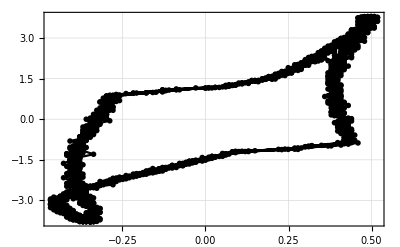

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Nekhaev_01.04.2019.xlsx"][[1]][[2;;All,2;;3]];
ListLinePlot[data,PlotTheme->"Detailed"]
```